Converges

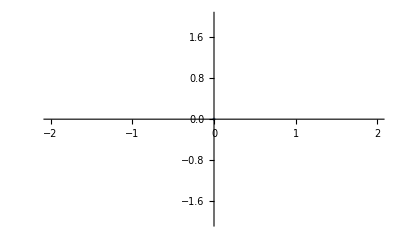

```mathematica
c=-0.65;
d=0.23;
z={{0,0}};
dt=1;
n=30;

f[c_,d_,n_,dt_]:=Module[{i,z={{0,0}}},
For[i=1,i<=n,i++,
If[z[[i,1]]^2+z[[i,2]]^2>2,Return[{"Diverges",i}]];
AppendTo[z,{z[[i,1]]+dt*(z[[i,1]]^2-z[[i,2]]^2-z[[i,1]]+c),z[[i,2]]+dt*(2*z[[i,1]]*z[[i,2]]-z[[i,2]]+d)}]
];
Return["Converges"]
]

f[c,d,n,dt]
ListPlot[z,PlotRange->{{-2,2},{-2,2}},PlotStyle->PointSize[0.005]]
```